```mathematica
SetDirectory[NotebookDirectory[]];
```

### Spectral densities

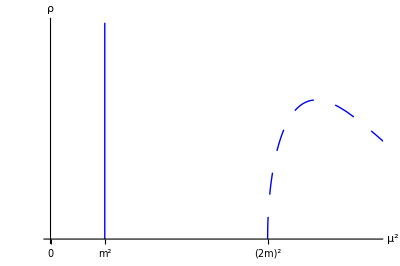

```mathematica
spectraldensitymassive=ParametricPlot[
{{1,t},{4+2t,3 √(t(t+4))Exp[-t(t+4)/4]}},{t,0,4},
PlotRange->{{0,6},{0,4}},
AxesLabel->{"μ^2","ρ"},Ticks->{{0,{1,"m^2"},{4,"(2m)^2"}},None},PlotStyle->{Directive[Blue,Thick],Directive[{Blue,Thick,Dashing[0.04]}]},
BaseStyle->{16,FontFamily->"Latin Modern Roman"}
]
```

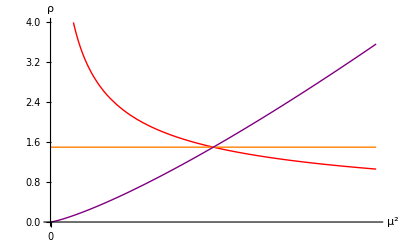

```mathematica
spectraldensityconformal=Plot[
{1.5(μ/3)^(-1/2),1.5,1.5(μ/3)^1.25},
{μ,0,6},
PlotRange->{{0,6},{0,4}},
AxesLabel->{"μ^2","ρ"},
Ticks->{{0},None},PlotStyle->{Directive[Red,Thick],Directive[Orange,Thick],Directive[Purple,Thick]},
BaseStyle->{16,FontFamily->"Latin Modern Roman"}]
```

```mathematica
Export["spectraldensity_massive.pdf",
spectraldensitymassive]
Export["spectraldensity_conformal.pdf",
spectraldensityconformal]
```

spectraldensity_massive.pdf

spectraldensity_conformal.pdf

### Foliations of Euclidean space

```mathematica
color=ColorData["DarkRainbow"];
```

```mathematica
circle[r_,θ_]:=r{Cos[θ],Sin[θ]}
```

```mathematica
nmax=6;
τ=2/3;
```

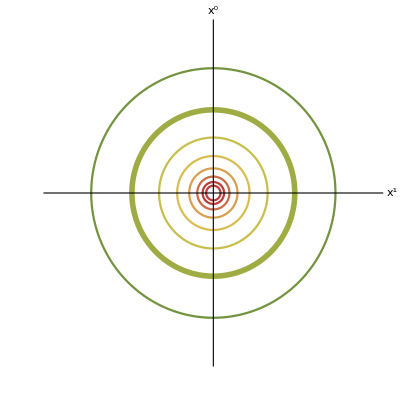

```mathematica
Rsurfaces=Table[circle[τ^n,θ],{n,-1,nmax}]//Simplify;
Rfoliation=ParametricPlot[
Rsurfaces,
{θ,0,2π},
PlotRange->{{-2,2},{-2,2}},
Ticks->None,
PlotStyle->Table[If[n==0,Directive[Thickness[0.01],color[1/2]],color[(nmax+n)/(2nmax)]],{n,-1,nmax}],
AxesLabel->{"x^1","x^0"},
BaseStyle->{16,FontFamily->"Latin Modern Roman"}
]
```

```mathematica
conformalmap[x_,y_]:={2x,x^2+y^2-1}/(x^2+(1+y)^2)
```

```mathematica
conformalmap[0,0]//Simplify
```

{0,-1}

```mathematica
Limit[conformalmap[x,y],y->∞]
Limit[conformalmap[x,y],x->∞]
```

{0,1}

{0,1}

```mathematica
conformalmap@@circle[1,θ]//Simplify
```

{Cos[θ]/(1+Sin[θ]),0}

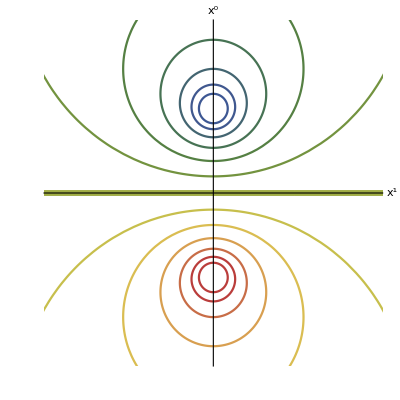

```mathematica
NSsurfaces=Table[conformalmap@@circle[τ^n,θ],{n,-nmax,nmax}]//Simplify;
NSfoliation=ParametricPlot[
NSsurfaces,
{θ,0,2π},
PlotRange->{{-2,2},{-2,2}},
Ticks->None,
AxesLabel->{"x^1","x^0"},
PlotStyle->Table[If[n==0,Directive[Thickness[0.01],color[1/2]],color[(nmax+n)/(2nmax)]],{n,-nmax,nmax}],
BaseStyle->{16,FontFamily->"Latin Modern Roman"}
]
```

```mathematica
Export["Rfoliation.pdf",Rfoliation]
Export["NSfoliation.pdf",NSfoliation]
```

Rfoliation.pdf

NSfoliation.pdf

### Regge trajectories

```mathematica
Δσ=0.5181489;
Δϵ=1.412625;
```

Spin and twist of the operators in various family:

```mathematica
OPEdataσ={{2,1},{4,1.02267},{6,1.02849},{8,1.03102},{10,1.03241},{12,1.03329},{14,1.03384},{16,1.03426},{18,1.03456},{20,1.03479},{22,1.03498},{24,1.03512},{26,1.03525},{28,1.03534},{30,1.03545},{32,1.03547},{34,1.03563},{36,1.03561},{38,1.03564},{40,1.03564}};
OPEdataσ2={{0,3.82968},{2,3.50915},{4,3.38568},{6,3.32032},{8,3.2751},{10,3.241},{12,3.2301},{14,3.1944},{16,3.195},{18,3.172},{20,3.167},{22,3.163},{24,3.1491},{26,3.146},{28,3.1306},{30,3.126},{32,3.1299},{34,3.1174},{36,3.1079},{38,3.101},{40,3.102},{42,3.116}};
OPEdataϵ={{4,2.42065},{6,2.4957},{8,2.562},{10,2.5659},{12,2.633},{14,2.6174},{16,2.678},{18,2.654},{20,2.651},{22,2.671},{24,2.681},{26,2.706},{28,2.6923},{30,2.702},{32,2.718},{34,2.717},{36,2.697},{38,2.701},{40,2.726},{42,2.729}};
OPEdataothers={{0,1.41263},{2,5.0758},{4,4.941},{6,4.975},{0,6.8956},{0,7.2535}};
```

```mathematica
OPEdata=Join[{{0,0}},OPEdataσ,OPEdataσ2,OPEdataϵ,OPEdataothers];
```

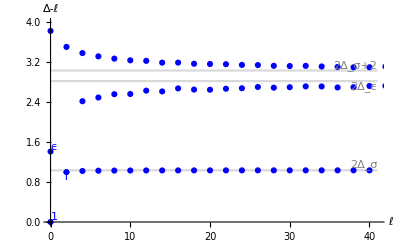

```mathematica
IsingSpectrum=Show[
Plot[
{2Δσ,2Δϵ,2Δσ+2},
{l,0,41},
PlotRange->{{0,41},{0,4}},
PlotStyle->LightGray,
AxesLabel->{"ℓ","Δ-ℓ"},
BaseStyle->{14,FontFamily->"Latin Modern Roman"}
],
ListPlot[
OPEdata,
PlotStyle->Blue
],
Graphics[{
Gray,
Text["2Δ_σ",{41,2Δσ},{1,-1.5}],
Text["2Δ_σ+2",{41,2Δσ+2},{1,-1.8}],
Text["2Δ_ϵ",{41,2Δϵ},{1,1.8}],
Blue,
Text["1",{0,0},{-3,-1}],
Text["ϵ",{0,Δϵ},{-3,-1}],
Text["T",{2,1},{0,1}]
}]
]
```

```mathematica
Export["IsingSpectrum.pdf",IsingSpectrum]
```

IsingSpectrum.pdf

### Conformal cylinder

```mathematica
zmax=3;
δ=-0.9 π/2;
view={0,12,4};
```

```mathematica
RadialQuantizationCylinder=Show[
ParametricPlot3D[
{Cos[θ+δ],Sin[θ+δ],z},
{θ,-π,π},{z,-zmax,zmax},
PlotRange->{{-1.2,1.2},{-1.2,1.2},{-zmax,zmax}},
PlotStyle->Directive[LightYellow,Opacity[0.4]],
Boxed->False,Axes->None,
Mesh->None,
ViewPoint->view,
BaseStyle->{16,FontFamily->"Latin Modern Roman"}],
ParametricPlot3D[{Cos[θ],Sin[θ],0},
{θ,0,2π},
PlotStyle->Blue],
Graphics3D[{
Blue,
Arrowheads[0.025],
Text["r = 1",{Cos[π+δ],Sin[π+δ],-0.2}],
Arrow[{{Cos[π+δ],Sin[π+δ],2.4},{Cos[π+δ],Sin[π+δ],2.8}}],
Text["r → ∞",{Cos[π+δ-0.4],Sin[π+δ-0.4],2.6}],
Arrow[{{Cos[π+δ],Sin[π+δ],-2.4},{Cos[π+δ],Sin[π+δ],-2.8}}],
Text["r = 0",{Cos[π+δ-0.4],Sin[π+δ-0.4],-2.6}],
Opacity[0],
Sphere[{Cos[δ],Sin[δ],0},0.04],
Sphere[{Cos[π+δ],Sin[π+δ],0},0.04]
}]
]
```

-Graphics3D-

```mathematica
NSQuantizationCylinder=Show[
ParametricPlot3D[
{Cos[θ+δ],Sin[θ+δ],z},
{θ,-π,π},{z,-zmax,zmax},
PlotRange->{{-1.2,1.2},{-1.2,1.2},{-zmax,zmax}},
PlotStyle->Directive[LightYellow,Opacity[0.4]],
Boxed->False,Axes->None,
Mesh->None,
ViewPoint->view,
BaseStyle->{16,FontFamily->"Latin Modern Roman"}],
ParametricPlot3D[{Cos[θ],Sin[θ],0},
{θ,0,2π},
PlotStyle->Blue],
Graphics3D[{
Blue,
Arrowheads[0.025],
Sphere[{Cos[π+δ],Sin[π+δ],0},0.04],
Text["0",{Cos[π+δ],Sin[π+δ],-0.2}],
Sphere[{Cos[δ],Sin[δ],0},0.04],
Text["∞",{Cos[δ],Sin[δ],0.2}],
Arrow[{{Cos[π+δ],Sin[π+δ],2.4},{Cos[π+δ],Sin[π+δ],2.8}}],
Text["(1,0)",{Cos[π+δ-0.4],Sin[π+δ-0.4],2.6}],
Arrow[{{Cos[π+δ],Sin[π+δ],-2.4},{Cos[π+δ],Sin[π+δ],-2.8}}],
Text["(-1,0)",{Cos[π+δ-0.5],Sin[π+δ-0.5],-2.6}],
}]
]
```

-Graphics3D-

```mathematica
LorentzianCylinder=Show[
ParametricPlot3D[
{Cos[θ+δ],Sin[θ+δ],z},
{θ,-π,π},{z,-(2θ)/π,(2θ)/π},
PlotRange->{{-1.2,1.2},{-1.2,1.2},{-zmax,zmax}},
PlotStyle->{LightBlue,Opacity[0.8]},
Boxed->False,Axes->None,
Mesh->None,
ViewPoint->view,
BaseStyle->{16,FontFamily->"Latin Modern Roman"}],
ParametricPlot3D[
{{Cos[θ+δ],Sin[θ+δ],z},{Cos[-θ+δ],Sin[-θ+δ],z},{Cos[θ+δ],Sin[θ+δ],-z},{Cos[-θ+δ],Sin[-θ+δ],-z}},
{θ,0,π},{z,(2θ)/π,zmax},
PlotStyle->Directive[LightYellow,Opacity[0.4]],
Mesh->None],
ParametricPlot3D[{Cos[θ],Sin[θ],0},
{θ,0,2π},
PlotStyle->Blue],
ParametricPlot3D[
{{Cos[θ+δ],Sin[θ+δ],(2θ)/π},{Cos[θ+δ],Sin[θ+δ],-(2θ)/π}},
{θ,-(3π)/2,(3π)/2},
PlotStyle->Black],
Graphics3D[{
Blue,
Sphere[{Cos[π+δ],Sin[π+δ],0},0.04],
Text["0",{Cos[π+δ],Sin[π+δ],-0.2}],
Sphere[{Cos[δ],Sin[δ],0},0.04],
Text["∞",{Cos[δ],Sin[δ],0.2}]
}]
]
```

-Graphics3D-

```mathematica
dpi=500;
Export["RCylinder.pdf",RadialQuantizationCylinder,ImageResolution->dpi]
Export["NSCylinder.pdf",NSQuantizationCylinder,ImageResolution->dpi]
Export["LorentzianCylinder.pdf",LorentzianCylinder,ImageResolution->dpi]
```

RCylinder.pdf

NSCylinder.pdf

LorentzianCylinder.pdf

### Crossing symmetry diagrams

```mathematica
ϕ1={-1,1};
ϕ2={-1,-1};
ϕ3={1,-1};
ϕ4={1,1};
v12={-1/2,0};
v34={1/2,0};
v14={0,1/2};
v23={0,-1/2};
```

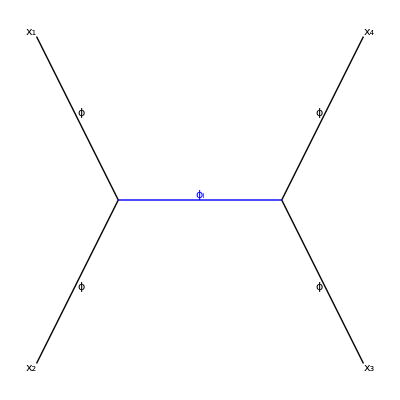

```mathematica
schannel=Graphics[{
PointSize[0.01],
Line[{ϕ1,v12,ϕ2}],
Line[{ϕ3,v34,ϕ4}],
Text["x_1",ϕ1,-ϕ1],
Text["x_2",ϕ2,-ϕ2],
Text["x_3",ϕ3,-ϕ3],
Text["x_4",ϕ4,-ϕ4],
Text["ϕ",(ϕ1+v12)/2,ϕ2],
Text["ϕ",(ϕ2+v12)/2,ϕ1],
Text["ϕ",(ϕ3+v34)/2,ϕ4],
Text["ϕ",(ϕ4+v34)/2,ϕ3],
Thick,Blue,
Line[{v12,v34}],
Text["ϕ_i",(v12+v34)/2,{0,-1}]
},BaseStyle->{36,FontFamily->"Latin Modern Roman"}]
```

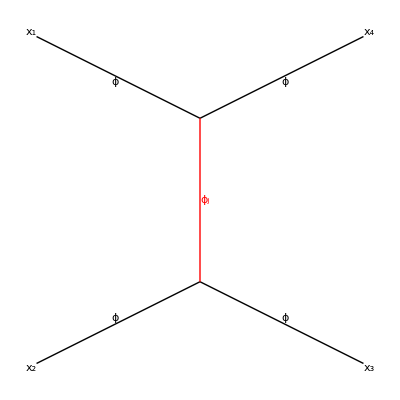

```mathematica
tchannel=Graphics[{
PointSize[0.01],
Line[{ϕ1,v14,ϕ4}],
Line[{ϕ2,v23,ϕ3}],
Text["x_1",ϕ1,-ϕ1],
Text["x_2",ϕ2,-ϕ2],
Text["x_3",ϕ3,-ϕ3],
Text["x_4",ϕ4,-ϕ4],
Text["ϕ",(ϕ1+v14)/2,ϕ4],
Text["ϕ",(ϕ4+v14)/2,ϕ1],
Text["ϕ",(ϕ2+v23)/2,ϕ3],
Text["ϕ",(ϕ3+v23)/2,ϕ2],
Thick,Red,
Line[{v14,v23}],
Text["ϕ_j",(v14+v23)/2,{-2,0}]
},BaseStyle->{36,FontFamily->"Latin Modern Roman"}]
```

```mathematica
Export["s-channel.pdf",schannel]
Export["t-channel.pdf",tchannel]
```

s-channel.pdf

t-channel.pdf

### Conformal frames

```mathematica
z=0.7Exp[I π/6];
```

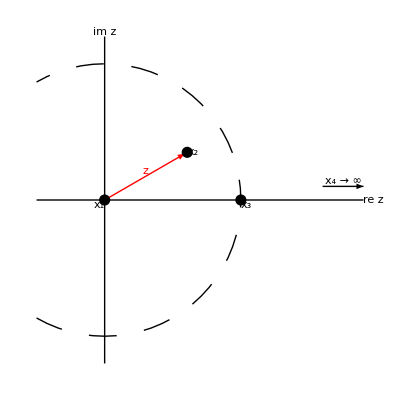

```mathematica
zplane=Graphics[{
Line[{{-0.5,0},{1.9,0}}],
Line[{{0,-1.2},{0,1.2}}],
Text["re z",{1.9,0},{-2,0}],
Text["im z",{0,1.2},{0,-1}],
Red,
Arrow[{{0,0},0.97{Re[z],Im[z]}}],
Text["z",1/2{Re[z],Im[z]},{0,-1}],
Black,
PointSize[0.02],
Point[{0,0}],
Text["x_1",{0,0},{1.5,1}],
Point[{1,0}],
Text["x_3",{1,0},{-1.5,1}],
Point[{Re[z],Im[z]}],
Text["x_2",{Re[z],Im[z]},{-2,0}],
Arrow[{{1.6,0.1},{1.9,0.1}}],
Text["x_4 → ∞",{1.75,0.1},{0,-1.5}],
Dashing[0.05],
Circle[{0,0},1,{-2π/3,2π/3}]
},BaseStyle->{24,FontFamily->"Latin Modern Roman"}]
```

```mathematica
ρ=0.6Exp[-I π/3];
```

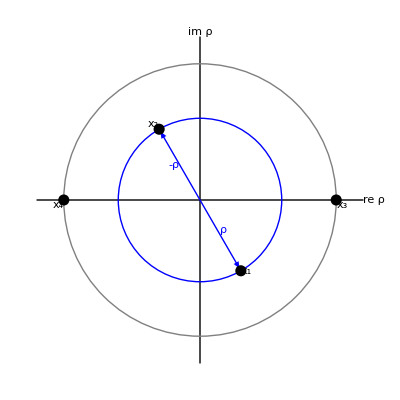

```mathematica
ρplane=Graphics[{
Line[{{-1.2,0},{1.2,0}}],
Line[{{0,-1.2},{0,1.2}}],
Text["re ρ",{1.2,0},{-2,0}],
Text["im ρ",{0,1.2},{0,-1}],
Gray,
Circle[{0,0},1],
Blue,
Circle[{0,0},Abs[ρ]],
Arrow[{{0,0},0.97{Re[ρ],Im[ρ]}}],
Text["ρ",1/2{Re[ρ],Im[ρ]},{-1.5,-1}],
Arrow[{{0,0},-0.97{Re[ρ],Im[ρ]}}],
Text["-ρ",-1/2{Re[ρ],Im[ρ]},{1.5,0}],
Black,
PointSize[0.02],
Point[{-1,0}],
Text["x_4",{-1,0},{1.5,1}],
Point[{1,0}],
Text["x_3",{1,0},{-1.5,1}],
Point[{Re[ρ],Im[ρ]}],
Text["x_1",{Re[ρ],Im[ρ]},{-2,0}],
Point[{-Re[ρ],-Im[ρ]}],
Text["x_2",{-Re[ρ],-Im[ρ]},{2,-1}]
},BaseStyle->{24,FontFamily->"Latin Modern Roman"}]
```

```mathematica
Export["z-plane.pdf",zplane]
Export["rho-plane.pdf",ρplane]
```

```mathematica
θ=-π/3;
```

```mathematica
ρcylinder=Show[
ParametricPlot3D[
{{1,0,3(t-1/2)},{-1,0,3(t-1/2)},{Cos[2π t],Sin[2π t],3/2},{Cos[π t],Sin[π t],-3/2},{Cos[π t],-Sin[π t],-3/2},{Cos[π t],Sin[π t],2/3},{Cos[π t],-Sin[π t],2/3},{Cos[π t],Sin[π t],-1/2},{Cos[π t],-Sin[π t],-1/2},{1-2t,0,-1/2},
{(1-2t)Cos[θ],(1-2t)Sin[θ],-1/2},
{-0.3Cos[t θ],-0.3Sin[t θ],-1/2}
},
{t,0,1},
PlotStyle->{Gray,Gray,Gray,Gray,Directive[Gray,Dashing[0.03]],Black,Directive[Black,Dashing[0.03]],Black,Directive[Black,Dashing[0.03]],Directive[Blue,Dashing[0.03]],Directive[Blue,Dashing[0.03]],Blue},
Boxed->False,Axes->False,
PlotRange->{{-1.2,1.2},{-1.2,1.2},{-1.6,1.6}},
ViewPoint->{0,10,3},
BaseStyle->{24,FontFamily->"Latin Modern Roman"}
],
Graphics3D[{
PointSize[0.03],
Point[{1,0.02,2/3}],
Point[{-1,0.02,2/3}],
Text["x_3",1.2{-1,0,2/3}],
Text["x_4",1.2{1,0,2/3}],
Point[{Cos[θ],Sin[θ],-1/2}],
Point[{Cos[π+θ],Sin[π+θ],-1/2}],
Text["x_1",1.1{Cos[π+θ],Sin[π+θ],-1/2-0.05}],
Text["x_2",1.1{Cos[θ],Sin[θ],-1/2+0.3}],
Blue,
Text["θ",{-0.1,0,-1/2-0.15}],
Text["τ = log(r)",{-0.3,0,0.15}],
Thick,
Line[{{Cos[(2θ)/3+π],Sin[(2θ)/3+π],-1/2},{Cos[(2θ)/3+π],Sin[(2θ)/3+π],2/3}}]
}]
]
```

-Graphics3D-

```mathematica
Export["rho-cylinder.pdf",ρcylinder]
```

rho-cylinder.pdf

### Convex optimization